### Start choosing the example:

```mathematica
t=27;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{10,15}},Switching Costs→{}|>

```mathematica
Data["Entrance Vertices and Currents"]={{1,80}};
Data["Exit Vertices and Terminal Costs"]={{10,15}};
```

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0&&j289-j300-u331+u342==0&&j290-j301-u332+u343==0&&j291-j302-u333+u344==0&&j292-j303-u334+u345==0&&j293-j304-u335+u346==0&&j294-j305-u336+u347==0&&j295-j306-u337+u348==0&&j296-j307-u338+u349==0&&j297-j308-u339+u350==0

EEX: -u331+u341==0.&&-80+u331-u332==0.&&-80+u332-u333==0.&&-80+u333-u334==0.&&-80+u334-u335==0.&&-80+u335-u336==0.&&-80+u336-u337==0.&&-80+u337-u338==0.&&-80+u338-u339==0.&&-95+u339==0.

D2E: {True,<|j299→80,u351→15,j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u340→15,u342→-80+735.,u343→-80+655.,u344→-80+575.,u345→-80+495.,u346→-80+415.,u347→-80+335.,u348→-80+255.,u349→-80+175.,u350→-80+95.,u352→735.,u331→735.,u332→655.,u333→575.,u334→495.,u335→415.,u336→335.,u337→255.,u338→175.,u339→95.,u341→735.|>}

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.031067,Null}

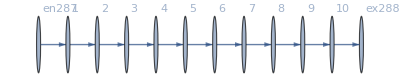

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→735.,u332→655.,u333→575.,u334→495.,u335→415.,u336→335.,u337→255.,u338→175.,u339→95.,u340→15,u341→735.,u342→-80+735.,u343→-80+655.,u344→-80+575.,u345→-80+495.,u346→-80+415.,u347→-80+335.,u348→-80+255.,u349→-80+175.,u350→-80+95.,u351→15,u352→735.|>

```mathematica
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{10,15}},Switching Costs→{}|>

#### Non-linear case

```mathematica
alpha = 0;
FFR= FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==77.418&&80.-u332+1. u333==77.418&&80.-u333+1. u334==77.418&&80.-u334+1. u335==77.418&&80.-u335+1. u336==77.418&&80.-u336+1. u337==77.418&&80.-u337+1. u338==77.418&&80.-u338+1. u339==77.418&&95.-u339==77.418

FRX1: The Error on the nonlinear terms is 2.66454×10^-15

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==77.418&&80.-u332+1. u333==77.418&&80.-u333+1. u334==77.418&&80.-u334+1. u335==77.418&&80.-u335+1. u336==77.418&&80.-u336+1. u337==77.418&&80.-u337+1. u338==77.418&&80.-u338+1. u339==77.418&&95.-u339==77.418

FRX1: The Error on the nonlinear terms is 2.66454×10^-15

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→38.2376,u332→35.6556,u333→33.0737,u334→30.4917,u335→27.9098,u336→25.3278,u337→22.7459,u338→20.1639,u339→17.582,u340→15,u341→0.+1. 38.2376,u342→0.+1. 35.6556,u343→0.+1. 33.0737,u344→0.+1. 30.4917,u345→0.+1. 27.9098,u346→0.+1. 25.3278,u347→0.+1. 22.7459,u348→0.+1. 20.1639,u349→0.+1. 17.582,u350→15.,u351→15,u352→0.+1. 38.2376|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==76.8387&&80.-u332+1. u333==76.8387&&80.-u333+1. u334==76.8387&&80.-u334+1. u335==76.8387&&80.-u335+1. u336==76.8387&&80.-u336+1. u337==76.8387&&80.-u337+1. u338==76.8387&&80.-u338+1. u339==76.8387&&95.-u339==76.8387

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==76.8387&&80.-u332+1. u333==76.8387&&80.-u333+1. u334==76.8387&&80.-u334+1. u335==76.8387&&80.-u335+1. u336==76.8387&&80.-u336+1. u337==76.8387&&80.-u337+1. u338==76.8387&&80.-u338+1. u339==76.8387&&95.-u339==76.8387

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→43.4521,u332→40.2907,u333→37.1294,u334→33.968,u335→30.8067,u336→27.6454,u337→24.484,u338→21.3227,u339→18.1613,u340→15,u341→0.+1. 43.4521,u342→0.+1. 40.2907,u343→0.+1. 37.1294,u344→0.+1. 33.968,u345→0.+1. 30.8067,u346→0.+1. 27.6454,u347→0.+1. 24.484,u348→0.+1. 21.3227,u349→0.+1. 18.1613,u350→15.,u351→15,u352→0.+1. 43.4521|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==74.9761&&80.-u332+1. u333==74.9761&&80.-u333+1. u334==74.9761&&80.-u334+1. u335==74.9761&&80.-u335+1. u336==74.9761&&80.-u336+1. u337==74.9761&&80.-u337+1. u338==74.9761&&80.-u338+1. u339==74.9761&&95.-u339==74.9761

FRX1: The Error on the nonlinear terms is 1.59872×10^-14

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==74.9761&&80.-u332+1. u333==74.9761&&80.-u333+1. u334==74.9761&&80.-u334+1. u335==74.9761&&80.-u335+1. u336==74.9761&&80.-u336+1. u337==74.9761&&80.-u337+1. u338==74.9761&&80.-u338+1. u339==74.9761&&95.-u339==74.9761

FRX1: The Error on the nonlinear terms is 1.59872×10^-14

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→60.215,u332→55.1911,u333→50.1672,u334→45.1433,u335→40.1195,u336→35.0956,u337→30.0717,u338→25.0478,u339→20.0239,u340→15,u341→0.+1. 60.215,u342→0.+1. 55.1911,u343→0.+1. 50.1672,u344→0.+1. 45.1433,u345→0.+1. 40.1195,u346→0.+1. 35.0956,u347→0.+1. 30.0717,u348→0.+1. 25.0478,u349→0.+1. 20.0239,u350→15.,u351→15,u352→0.+1. 60.215|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==35.034&&80.-u332+1. u333==35.034&&80.-u333+1. u334==35.034&&80.-u334+1. u335==35.034&&80.-u335+1. u336==35.034&&80.-u336+1. u337==35.034&&80.-u337+1. u338==35.034&&80.-u338+1. u339==35.034&&95.-u339==35.034

FRX1: The Error on the nonlinear terms is 0.

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==35.034&&80.-u332+1. u333==35.034&&80.-u333+1. u334==35.034&&80.-u334+1. u335==35.034&&80.-u335+1. u336==35.034&&80.-u336+1. u337==35.034&&80.-u337+1. u338==35.034&&80.-u338+1. u339==35.034&&95.-u339==35.034

FRX1: The Error on the nonlinear terms is 0.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→419.694,u332→374.728,u333→329.762,u334→284.796,u335→239.83,u336→194.864,u337→149.898,u338→104.932,u339→59.966,u340→15,u341→0.+1. 419.694,u342→0.+1. 374.728,u343→0.+1. 329.762,u344→0.+1. 284.796,u345→0.+1. 239.83,u346→0.+1. 194.864,u347→0.+1. 149.898,u348→0.+1. 104.932,u349→0.+1. 59.966,u350→15.,u351→15,u352→0.+1. 419.694|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==0&&80.-u332+1. u333==0&&80.-u333+1. u334==0&&80.-u334+1. u335==0&&80.-u335+1. u336==0&&80.-u336+1. u337==0&&80.-u337+1. u338==0&&80.-u338+1. u339==0&&95.-u339==0

FRX1: The Error on the nonlinear terms is 2.55795×10^-13

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→735.,u332→655.,u333→575.,u334→495.,u335→415.,u336→335.,u337→255.,u338→175.,u339→95.,u340→15,u341→0.+1. 735.,u342→0.+1. 655.,u343→0.+1. 575.,u344→0.+1. 495.,u345→0.+1. 415.,u346→0.+1. 335.,u347→0.+1. 255.,u348→0.+1. 175.,u349→0.+1. 95.,u350→15.,u351→15,u352→0.+1. 735.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-283.906&&80.-u332+1. u333==-283.906&&80.-u333+1. u334==-283.906&&80.-u334+1. u335==-283.906&&80.-u335+1. u336==-283.906&&80.-u336+1. u337==-283.906&&80.-u337+1. u338==-283.906&&80.-u338+1. u339==-283.906&&95.-u339==-283.906

FRX1: The Error on the nonlinear terms is 5.3626×10^-13

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-283.906&&80.-u332+1. u333==-283.906&&80.-u333+1. u334==-283.906&&80.-u334+1. u335==-283.906&&80.-u335+1. u336==-283.906&&80.-u336+1. u337==-283.906&&80.-u337+1. u338==-283.906&&80.-u338+1. u339==-283.906&&95.-u339==-283.906

FRX1: The Error on the nonlinear terms is 5.3626×10^-13

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→3290.15,u332→2926.25,u333→2562.34,u334→2198.43,u335→1834.53,u336→1470.62,u337→1106.72,u338→742.811,u339→378.906,u340→15,u341→0.+1. 3290.15,u342→0.+1. 2926.25,u343→0.+1. 2562.34,u344→0.+1. 2198.43,u345→0.+1. 1834.53,u346→0.+1. 1470.62,u347→0.+1. 1106.72,u348→0.+1. 742.811,u349→0.+1. 378.906,u350→15.,u351→15,u352→0.+1. 3290.15|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-22760.5&&80.-u332+1. u333==-22760.5&&80.-u333+1. u334==-22760.5&&80.-u334+1. u335==-22760.5&&80.-u335+1. u336==-22760.5&&80.-u336+1. u337==-22760.5&&80.-u337+1. u338==-22760.5&&80.-u338+1. u339==-22760.5&&95.-u339==-22760.5

FRX1: The Error on the nonlinear terms is 0.

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-22760.5&&80.-u332+1. u333==-22760.5&&80.-u333+1. u334==-22760.5&&80.-u334+1. u335==-22760.5&&80.-u335+1. u336==-22760.5&&80.-u336+1. u337==-22760.5&&80.-u337+1. u338==-22760.5&&80.-u338+1. u339==-22760.5&&95.-u339==-22760.5

FRX1: The Error on the nonlinear terms is 0.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→205579.,u332→182739.,u333→159898.,u334→137058.,u335→114217.,u336→91376.9,u337→68536.4,u338→45695.9,u339→22855.5,u340→15,u341→0.+1. 205579.,u342→0.+1. 182739.,u343→0.+1. 159898.,u344→0.+1. 137058.,u345→0.+1. 114217.,u346→0.+1. 91376.9,u347→0.+1. 68536.4,u348→0.+1. 45695.9,u349→0.+1. 22855.5,u350→15.,u351→15,u352→0.+1. 205579.|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-289963.&&80.-u332+1. u333==-289963.&&80.-u333+1. u334==-289963.&&80.-u334+1. u335==-289963.&&80.-u335+1. u336==-289963.&&80.-u336+1. u337==-289963.&&80.-u337+1. u338==-289963.&&80.-u338+1. u339==-289963.&&95.-u339==-289963.

FRX1: The Error on the nonlinear terms is 0.

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-289963.&&80.-u332+1. u333==-289963.&&80.-u333+1. u334==-289963.&&80.-u334+1. u335==-289963.&&80.-u335+1. u336==-289963.&&80.-u336+1. u337==-289963.&&80.-u337+1. u338==-289963.&&80.-u338+1. u339==-289963.&&95.-u339==-289963.

FRX1: The Error on the nonlinear terms is 0.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→2.6104×10^6,u332→2.32036×10^6,u333→2.03032×10^6,u334→1.74027×10^6,u335→1.45023×10^6,u336→1.16019×10^6,u337→870144.,u338→580101.,u339→290058.,u340→15,u341→0.+1. 2.6104×10^6,u342→0.+1. 2.32036×10^6,u343→0.+1. 2.03032×10^6,u344→0.+1. 1.74027×10^6,u345→0.+1. 1.45023×10^6,u346→0.+1. 1.16019×10^6,u347→0.+1. 870144.,u348→0.+1. 580101.,u349→0.+1. 290058.,u350→15.,u351→15,u352→0.+1. 2.6104×10^6|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-290863.&&80.-u332+1. u333==-290863.&&80.-u333+1. u334==-290863.&&80.-u334+1. u335==-290863.&&80.-u335+1. u336==-290863.&&80.-u336+1. u337==-290863.&&80.-u337+1. u338==-290863.&&80.-u338+1. u339==-290863.&&95.-u339==-290863.

FRX1: The Error on the nonlinear terms is 0.

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-290863.&&80.-u332+1. u333==-290863.&&80.-u333+1. u334==-290863.&&80.-u334+1. u335==-290863.&&80.-u335+1. u336==-290863.&&80.-u336+1. u337==-290863.&&80.-u337+1. u338==-290863.&&80.-u338+1. u339==-290863.&&95.-u339==-290863.

FRX1: The Error on the nonlinear terms is 0.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→2.6185×10^6,u332→2.32756×10^6,u333→2.03661×10^6,u334→1.74567×10^6,u335→1.45473×10^6,u336→1.16379×10^6,u337→872843.,u338→581900.,u339→290958.,u340→15,u341→0.+1. 2.6185×10^6,u342→0.+1. 2.32756×10^6,u343→0.+1. 2.03661×10^6,u344→0.+1. 1.74567×10^6,u345→0.+1. 1.45473×10^6,u346→0.+1. 1.16379×10^6,u347→0.+1. 872843.,u348→0.+1. 581900.,u349→0.+1. 290958.,u350→15.,u351→15,u352→0.+1. 2.6185×10^6|>

```mathematica
alpha = 1.605;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-339107.&&80.-u332+1. u333==-339107.&&80.-u333+1. u334==-339107.&&80.-u334+1. u335==-339107.&&80.-u335+1. u336==-339107.&&80.-u336+1. u337==-339107.&&80.-u337+1. u338==-339107.&&80.-u338+1. u339==-339107.&&95.-u339==-339107.

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→735.,u332→655.,u333→575.,u334→495.,u335→415.,u336→335.,u337→255.,u338→175.,u339→95.,u340→15,u341→735.,u342→-80+735.,u343→-80+655.,u344→-80+575.,u345→-80+495.,u346→-80+415.,u347→-80+335.,u348→-80+255.,u349→-80+175.,u350→-80+95.,u351→15,u352→735.|>

```mathematica
alpha = 1.61;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-397981.&&80.-u332+1. u333==-397981.&&80.-u333+1. u334==-397981.&&80.-u334+1. u335==-397981.&&80.-u335+1. u336==-397981.&&80.-u336+1. u337==-397981.&&80.-u337+1. u338==-397981.&&80.-u338+1. u339==-397981.&&95.-u339==-397981.

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→735.,u332→655.,u333→575.,u334→495.,u335→415.,u336→335.,u337→255.,u338→175.,u339→95.,u340→15,u341→735.,u342→-80+735.,u343→-80+655.,u344→-80+575.,u345→-80+495.,u346→-80+415.,u347→-80+335.,u348→-80+255.,u349→-80+175.,u350→-80+95.,u351→15,u352→735.|>

```mathematica
alpha = 1.62;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-554286.&&80.-u332+1. u333==-554286.&&80.-u333+1. u334==-554286.&&80.-u334+1. u335==-554286.&&80.-u335+1. u336==-554286.&&80.-u336+1. u337==-554286.&&80.-u337+1. u338==-554286.&&80.-u338+1. u339==-554286.&&95.-u339==-554286.

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→735.,u332→655.,u333→575.,u334→495.,u335→415.,u336→335.,u337→255.,u338→175.,u339→95.,u340→15,u341→735.,u342→-80+735.,u343→-80+655.,u344→-80+575.,u345→-80+495.,u346→-80+415.,u347→-80+335.,u348→-80+255.,u349→-80+175.,u350→-80+95.,u351→15,u352→735.|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-1.65381×10^6&&80.-u332+1. u333==-1.65381×10^6&&80.-u333+1. u334==-1.65381×10^6&&80.-u334+1. u335==-1.65381×10^6&&80.-u335+1. u336==-1.65381×10^6&&80.-u336+1. u337==-1.65381×10^6&&80.-u337+1. u338==-1.65381×10^6&&80.-u338+1. u339==-1.65381×10^6&&95.-u339==-1.65381×10^6

FRX1: The Error on the nonlinear terms is 0.

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-1.65381×10^6&&80.-u332+1. u333==-1.65381×10^6&&80.-u333+1. u334==-1.65381×10^6&&80.-u334+1. u335==-1.65381×10^6&&80.-u335+1. u336==-1.65381×10^6&&80.-u336+1. u337==-1.65381×10^6&&80.-u337+1. u338==-1.65381×10^6&&80.-u338+1. u339==-1.65381×10^6&&95.-u339==-1.65381×10^6

FRX1: The Error on the nonlinear terms is 0.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→1.4885×10^7,u332→1.32311×10^7,u333→1.15772×10^7,u334→9.92335×10^6,u335→8.26946×10^6,u336→6.61557×10^6,u337→4.96168×10^6,u338→3.30779×10^6,u339→1.6539×10^6,u340→15,u341→0.+1. 1.4885×10^7,u342→0.+1. 1.32311×10^7,u343→0.+1. 1.15772×10^7,u344→0.+1. 9.92335×10^6,u345→0.+1. 8.26946×10^6,u346→0.+1. 6.61557×10^6,u347→0.+1. 4.96168×10^6,u348→0.+1. 3.30779×10^6,u349→0.+1. 1.6539×10^6,u350→15.,u351→15,u352→0.+1. 1.4885×10^7|>

```mathematica
alpha = 1.7;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-1.55949×10^7&&80.-u332+1. u333==-1.55949×10^7&&80.-u333+1. u334==-1.55949×10^7&&80.-u334+1. u335==-1.55949×10^7&&80.-u335+1. u336==-1.55949×10^7&&80.-u336+1. u337==-1.55949×10^7&&80.-u337+1. u338==-1.55949×10^7&&80.-u338+1. u339==-1.55949×10^7&&95.-u339==-1.55949×10^7

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→735.,u332→655.,u333→575.,u334→495.,u335→415.,u336→335.,u337→255.,u338→175.,u339→95.,u340→15,u341→735.,u342→-80+735.,u343→-80+655.,u344→-80+575.,u345→-80+495.,u346→-80+415.,u347→-80+335.,u348→-80+255.,u349→-80+175.,u350→-80+95.,u351→15,u352→735.|>

```mathematica
alpha = 1.8;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-2.40526×10^10&&80.-u332+1. u333==-2.40526×10^10&&80.-u333+1. u334==-2.40526×10^10&&80.-u334+1. u335==-2.40526×10^10&&80.-u335+1. u336==-2.40526×10^10&&80.-u336+1. u337==-2.40526×10^10&&80.-u337+1. u338==-2.40526×10^10&&80.-u338+1. u339==-2.40526×10^10&&95.-u339==-2.40526×10^10

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→735.,u332→655.,u333→575.,u334→495.,u335→415.,u336→335.,u337→255.,u338→175.,u339→95.,u340→15,u341→735.,u342→-80+735.,u343→-80+655.,u344→-80+575.,u345→-80+495.,u346→-80+415.,u347→-80+335.,u348→-80+255.,u349→-80+175.,u350→-80+95.,u351→15,u352→735.|>

```mathematica
alpha = 1.9;
FFR=Catch@FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-5.6037×10^18&&80.-u332+1. u333==-5.6037×10^18&&80.-u333+1. u334==-5.6037×10^18&&80.-u334+1. u335==-5.6037×10^18&&80.-u335+1. u336==-5.6037×10^18&&80.-u336+1. u337==-5.6037×10^18&&80.-u337+1. u338==-5.6037×10^18&&80.-u338+1. u339==-5.6037×10^18&&95.-u339==-5.6037×10^18

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→735.,u332→655.,u333→575.,u334→495.,u335→415.,u336→335.,u337→255.,u338→175.,u339→95.,u340→15,u341→735.,u342→-80+735.,u343→-80+655.,u344→-80+575.,u345→-80+495.,u346→-80+415.,u347→-80+335.,u348→-80+255.,u349→-80+175.,u350→-80+95.,u351→15,u352→735.|>

```mathematica
alpha = 2;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j300==jt311&&j299==jt312&&j289==jt313&&j301==jt314&&j290==jt315&&j302==jt316&&j291==jt317&&j303==jt318&&j292==jt319&&j304==jt320&&j293==jt321&&j305==jt322&&j294==jt323&&j306==jt324&&j295==jt325&&j307==jt326&&j296==jt327&&j308==jt328&&j297==jt329&&j309==jt330&&j289==jt312&&j310==jt311&&j300==jt314&&j290==jt313&&j301==jt316&&j291==jt315&&j302==jt318&&j292==jt317&&j303==jt320&&j293==jt319&&j304==jt322&&j294==jt321&&j305==jt324&&j295==jt323&&j306==jt326&&j296==jt325&&j307==jt328&&j297==jt327&&j308==jt330&&j298==jt329&&j299==80&&u351==15&&-u341+u352==0&&-u340+u351==0&&jt311==0&&jt330==0

EEX: -u331+u341==0.&&-u332+u342==0.&&-u333+u343==0.&&-u334+u344==0.&&-u335+u345==0.&&-u336+u346==0.&&-u337+u347==0.&&-u338+u348==0.&&-u339+u349==0.&&-15+u350==0.

EEX: 80.-u331+1. u332==-2.2049×10^106&&80.-u332+1. u333==-2.2049×10^106&&80.-u333+1. u334==-2.2049×10^106&&80.-u334+1. u335==-2.2049×10^106&&80.-u335+1. u336==-2.2049×10^106&&80.-u336+1. u337==-2.2049×10^106&&80.-u337+1. u338==-2.2049×10^106&&80.-u338+1. u339==-2.2049×10^106&&95.-u339==-2.2049×10^106

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j289→80,j290→80,j291→80,j292→80,j293→80,j294→80,j295→80,j296→80,j297→80,j298→80,j299→80,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j310→0,jt311→0,jt312→80,jt313→80,jt314→0,jt315→80,jt316→0,jt317→80,jt318→0,jt319→80,jt320→0,jt321→80,jt322→0,jt323→80,jt324→0,jt325→80,jt326→0,jt327→80,jt328→0,jt329→80,jt330→0,u331→735.,u332→655.,u333→575.,u334→495.,u335→415.,u336→335.,u337→255.,u338→175.,u339→95.,u340→15,u341→735.,u342→-80+735.,u343→-80+655.,u344→-80+575.,u345→-80+495.,u346→-80+415.,u347→-80+335.,u348→-80+255.,u349→-80+175.,u350→-80+95.,u351→15,u352→735.|>

### What we this plot for?

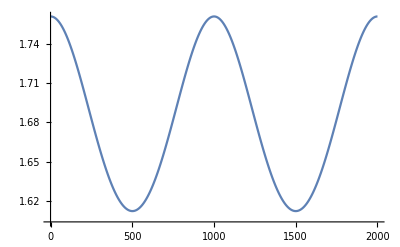

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.